## Steps for city generation

1. Start with a random base using a noise randomizer
	a. need to decide structure
	b. possible choices: tiling with each tile representing a different thing, polygons(nodes from that one article) 
2. From the base, generate more of the city
	a. Again we can use the nodes article where we can classify areas
	b. We can use wave function collapse: https://community.wolfram.com/groups/-/m/t/2435403
		wave function collapse is supposed to be easily compatible due to allowing support constraints so try my best to do that
* if we have extra time, add an option to be able to manually choose which base structure we start with.

possible tiles:
- street
- road
- building

### Perlin noise function(generating base city)

```mathematica
permutation = RandomSample[Range[1, 255]];
p = Join[permutation, permutation]; (*repeat it to avoid overflow*)
repeat = 255;
fade[t_] := t*t*t*(t*(t*6-15)+10); (* THE FADE FUNCTION >:) *)
inc[n_] := Module[{num = n+1}, If[repeat >0, num = Mod[num, repeat]]];
grad[hash_, x_, y_, z_] := Module[{hashy = BitAnd[hash,15 ]}, 
Which[
hashy==0, x+y,
hashy==1, -x+y,
hashy==2, x-y,
hashy==3, -x-y,
hashy==4, x+z,
hashy==5, -x+z,
hashy==6, x-z,
hashy==7, -x-z,
hashy==8, y+z,
hashy==9, -y+z,
hashy==10, y-z,
hashy==11,-y-z,
hashy==12,y+x,
hashy==13,-y+z,
hashy==14,y-x,
hashy==15,-y-z]];
lerp[a_,b_,x_] :=a+x*(b-a);
```

```mathematica
perlin[a_, b_, c_] := Module[{xi = Min[Floor[a], 254], yi = Min[Floor[b], 254], zi = Min[Floor[c], 254], aaa, aba, aab, abb, baa, bba, bab, bbb, x1, x2, y1, y2, x=a, y=b, z=c, xf, yf, zf, u, v, w},If[repeat> 0,{ x = Mod[a, repeat], y = Mod[b, repeat], z = Mod[c, repeat]}];  
xf = x-Floor[x];yf = y-Floor[y];zf = z-Floor[z]; 
u = fade[xf]; v = fade[yf]; w = fade[zf];
aaa =p[[p[[p[[        xi   +1]]+yi+1]]+        zi    +1]]; aba = p[[p[[p[[xi+1]]+inc[yi]+1]]+zi+1]]; aab=p[[p[[p[[         xi   +1]]+yi+1]]+inc[zi]+1]]; abb=p[[p[[p[[xi+1]]+inc[yi]+1]]+inc[zi]+1]]; baa=p[[p[[p[[inc[xi]+1]]+yi+1]]+          zi  +1]]; bba=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+zi+1]]; bab=p[[p[[p[[inc[xi]+1]]+yi+1]]+inc[zi]+1]]; bbb=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+inc[zi]+1]];
x1 = lerp[grad[aaa,xf,yf,zf],grad[baa,xf-1,yf,zf], u];
x2 = lerp[grad[aba, xf, yf-1, zf], grad[bba, xf-1, yf-1, zf],u];
y1 = lerp[x1, x2, v];
x1 = lerp[grad[aab, xf, yf, zf-1], grad[bab, xf-1, yf, zf-1], u];
x2 = lerp[grad[abb, xf, yf-1, zf-1], grad[abb, xf, yf-1, zf-1], u];
y2 = lerp[x1, x2, v];
Rescale[lerp[y1, y2, w], {-1.2, 1.2}]];
```

```mathematica
octavePerlin[x_,y_,z_,octaves_,persistence_]:=Module[{total=0, frequency=1,amplitude=1,maxValue=0},
total = perlin[x*frequency,y*frequency,z*frequency]*amplitude + Total[Table[maxValue+= amplitude;amplitude*=persistence;frequency*=2;perlin[x*frequency,y*frequency,z*frequency]*amplitude, {i,octaves-1}]]; total/maxValue];
```

```mathematica
octaves=RandomInteger[{2, 3}];persistence=RandomReal[{0.2,0.4}];
ex = Table[octavePerlin[RandomInteger[{0, 10}], RandomInteger[{0, 10}], RandomReal[{0, 10}], octaves, persistence], 10];
Max[ex]
Min[ex]
Mean[ex]
```

```mathematica
perlin[1,2,0.010]
```

0.495837

```mathematica
Plot3D[octavePerlin[x,y,0.05,6,0.6],{x,20,21},{y,10,11}]
```

-Graphics3D-

### Road generation(binary recursion+perlin noise)

```mathematica
generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=Module[{stack,roads={},noise,smoothstep,jitter,clamp,pickAxis,addVerticalRoad,addHorizontalRoad,pushChildren,roadAdded=False, sizeFactor},
    
  noise[x_,z_]:=octavePerlin[x*noiseFreq,z*noiseFreq,0,4,0.5];
  
  smoothstep[low_,high_,x_]:=Module[{t},t=Clip[(x-low)/(high-low),{0,1}]; t*t*(3-2*t)];
  
  jitter[max_]:=RandomReal[{-max,max}];
  
  clamp[val_,min_,max_]:=Min[Max[val,min],max];
  
  pickAxis[R_]:=If[R[[3]]>R[[4]],"vertical","horizontal"];
  
  addVerticalRoad[x_,yStart_,yEnd_,width_]:=(AppendTo[roads,{Max[x, 1],Max[yStart, 1],Max[x, 1],yEnd,width}]; roadAdded=True);
  
  addHorizontalRoad[xStart_,y_,xEnd_,width_]:=(AppendTo[roads,{Max[xStart, 1],Max[y, 1],xEnd,Max[y, 1],width}]; roadAdded=True);
  
  pushChildren[R_,xSplit_,ySplit_,dir_]:=
   If[dir=="vertical",
    AppendTo[stack,{R[[1]],R[[2]],xSplit-R[[1]],R[[4]]}];
    AppendTo[stack,{xSplit,R[[2]],R[[3]]+R[[1]]-xSplit,R[[4]]}],
    AppendTo[stack,{R[[1]],R[[2]],R[[3]],ySplit-R[[2]]}];
    AppendTo[stack,{R[[1]],ySplit,R[[3]],R[[4]]+R[[2]]-ySplit}]
    ];

  stack={{0,0,worldWidth,worldHeight}};

  While[Length[stack]>0,
   Module[{R,n,Psplit,dir,xSplit,ySplit},
    R=First[stack];
    stack=Rest[stack];
    
    n=noise[R[[1]]+R[[3]]/2,R[[2]]+R[[4]]/2];
sizeFactor=Min[(R[[3]]/minBlock)+(R[[4]]/minBlock),2];
(*sizeFactor=Echo[smoothstep[1,2,Min[R[[3]]/minBlock,R[[4]]/minBlock]]];*)
(*sizeFactor=1;*)
    Psplit=smoothstep[lowCutoff,highCutoff,n]*sizeFactor;
    If[RandomReal[]>Psplit,Continue[]];
    
    If[R[[3]]<2*minBlock||R[[4]]<2*minBlock,Continue[]];
    
    dir=pickAxis[R];
    
    If[dir=="vertical",
     xSplit=clamp[R[[1]]+R[[3]]/2+jitter[maxJitter],R[[1]]+minBlock,R[[1]]+R[[3]]-minBlock];
     addVerticalRoad[xSplit,R[[2]],R[[2]]+R[[4]],roadWidth];
     pushChildren[R,xSplit,Null,dir],
     ySplit=clamp[R[[2]]+R[[4]]/2+jitter[maxJitter],R[[2]]+minBlock,R[[2]]+R[[4]]-minBlock];
     addHorizontalRoad[R[[1]],ySplit,R[[1]]+R[[3]],roadWidth];
     pushChildren[R,Null,ySplit,dir]
     ];
    ];
   ];
  
  (* Ensure at least one road is added *)
  If[!roadAdded,
   dir=pickAxis[{0,0,worldWidth,worldHeight}];
   If[dir=="vertical",
    xSplit=clamp[worldWidth/2+jitter[maxJitter],minBlock,worldWidth-minBlock];
    addVerticalRoad[xSplit,0,worldHeight,roadWidth],
    ySplit=clamp[worldHeight/2+jitter[maxJitter],minBlock,worldHeight-minBlock];
    addHorizontalRoad[0,ySplit,worldWidth,roadWidth]
    ];
   ];
  
  roads
  ]
```

## Map Generation(appl of funcs)

```mathematica
worldWidth=100;
worldHeight=100;
minBlock=15;
maxJitter=5;
roadWidth=2;
noiseFreq=0.1;
lowCutoff=0.2;
highCutoff=0.8;
MapGrid = Table[0, {x, worldWidth}, {y, worldHeight}];
```

### Entity filling (parks, building, etc .) w/noisemap

0.551531

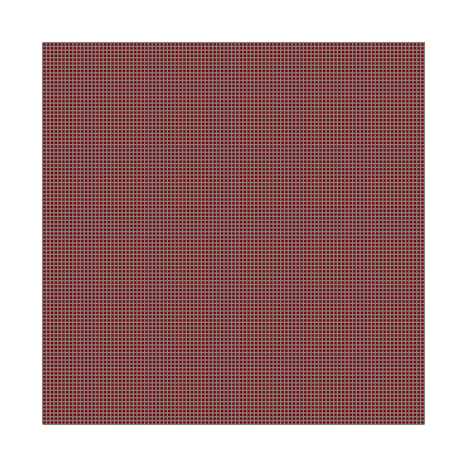

```mathematica
z=RandomReal[{0,255}];
octaves=6;
persistence=RandomReal[{0.5, 0.6}]
xcoef=RandomInteger[{0, 100}];ycoef=RandomInteger[{0,100}];
offset={0.37, 0.57};
(*noiseMap=Table[Mean[Flatten[Table[octavePerlin[a, b,z,octaves,persistence ], {a, x, x+10},{b, y, y+10}]]], {x, 1,100, 10},{y,1,100, 10}]*)
noiseMap=Table[octavePerlin[x+offset[[1]],y+0offset[[2]],z,octaves,persistence ],{x,xcoef,xcoef+5,0.05},{y,ycoef,ycoef+5,0.05}];
(*NEED TO FIGURE HOW TO MAKE THE NOISE THINGY ACC OKISH*)
classifyEntityTile[val_]:=Which[val<0.485,"park", val<0.52,"building", True, "background"];

tileColors=<|"road"->Black,"background"->White,"park" -> Green, "building"->Blue|>;
tileToNumber=AssociationThread[Keys[tileColors],Range[Length[tileColors]]];
tileMap=Map[classifyEntityTile,noiseMap,{2}];
MapGrid=Map[tileToNumber,tileMap,{2}];
(*numericGrid[[All,mid]]=1;*)

(*visualizeTileMap[tileMap_]:=Module[{tileColors=<|"road"->Gray,"building"->Darker[Red],"park"->LightGreen|>,tileNums,colorRules},tileNums=AssociationThread[Keys@tileColors,Range@Length@tileColors];
colorRules=Thread[Values@tileNums->Values@tileColors];
ArrayPlot[tileNums/@tileMap,ColorRules->colorRules,Frame->False,Mesh->True,MeshStyle->Gray]];*)

ArrayPlot[MapGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False,Mesh->True,MeshStyle->Gray]
```

### Street/Road Structure generation(grid format)

```mathematica
roadsCoords = generateRoads[worldWidth,worldHeight,minBlock,maxJitter,roadWidth,noiseFreq,lowCutoff,highCutoff];
(*For[i=1, i<=Length[roadsCoords], i++,
Module[{x1=roadsCoords[[]][[1]], x2=roadsCoords[[3]],y1=roadsCoords[[2]],y2=roadsCoords[[4]], width=roadsCoords[[5]]},If[x1==x2,MapGrid=ReplacePart[MapGrid,{x1,j_}/;y1<j<y2->"R"],MapGrid=ReplacePart[MapGrid,{i_,y|1}/;x1<i<x2->"R"] ]]];*)
roadPutter[Coords_] := Module[{x1=Coords[[1]]//Floor, x2=Coords[[3]]//Floor,y1=Coords[[2]]//Floor,y2=Coords[[4]]//Floor, width=Coords[[5]]},If[x1==x2,MapGrid=ReplacePart[MapGrid,{x1,j_}/;y1<=j<=y2->1],MapGrid=ReplacePart[MapGrid,{i_,y1}/;x1<=i<=x2->1] ]];
roadPutter/@roadsCoords;
MapGrid//Grid;
```

### Visualize

```mathematica
ArrayPlot[MapGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False(*,Mesh->True*)(*,MeshStyle->Gray*)]
```

Values::invrl: The argument tileToNumber is not a valid Association or a list of rules.

Values::invrl: The argument tileColors is not a valid Association or a list of rules.

-Graphics-

### zero blocks finder

```mathematica
visited=MapGrid;
zeroBlocks={};
findDownRight[x_,y_,grid_]:=Module[{i=x,j=y},
If[visited[[x,y]]==0,
Until[i>worldWidth,If[grid[[i,j]]!=1,i++,Break[]]];i--;Until[j>worldHeight,If[grid[[i,j]]!=1,j++,Break[]]];j--;visited=ReplacePart[visited,{a_,b_} /; x<=a<=i&&y<=b<=j->1];
AppendTo[zeroBlocks,{x, y, i, j}]]];

Table[findDownRight[x, y, MapGrid],{x,worldWidth},{y,worldHeight}];
zeroBlocks
```

{{1,1,25,44},{1,46,46,69},{1,71,46,72},{1,74,46,100},{27,1,45,44},{47,1,71,44},{48,46,52,72},{48,75,52,100},{54,46,100,73},{54,75,100,100},{73,1,100,44}}

### zeroblocks assigner

#### zeroblock testing

```mathematica
zeroBlocks={}
findDownRight[8, 2, MapGrid]
```

{}

9 2

10 2

11 2

{{8,2,10,3}}

```mathematica
|
```

```mathematica
MapGrid
```

{{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{1,1,1,1,1,1,1,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,1,0,0,1,0,0,0}}

```mathematica
MapGrid//Grid
```

0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0

```mathematica
Position[MapGrid,0]
```

{{1,1},{1,2},{1,5},{1,6},{1,8},{1,9},{1,10},{2,1},{2,2},{2,5},{2,6},{2,8},{2,9},{2,10},{3,1},{3,2},{3,5},{3,6},{3,8},{3,9},{3,10},{4,1},{4,2},{4,5},{4,6},{4,8},{4,9},{4,10},{5,1},{5,2},{5,5},{5,6},{5,8},{5,9},{5,10},{6,1},{6,2},{6,5},{6,6},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,1},{8,2},{8,3},{8,5},{8,6},{8,8},{8,9},{8,10},{9,1},{9,2},{9,3},{9,5},{9,6},{9,8},{9,9},{9,10},{10,1},{10,2},{10,3},{10,5},{10,6},{10,8},{10,9},{10,10}}

```mathematica
If[TRue,fefef]
```

```mathematica
#==1
```

```mathematica
Apply
0001
0001
0001
1111
0000

1111
1111
1111
1111
0000
```

## cool image visualization(on hold)

```mathematica
z=RandomReal[{0,255}];
octaves=6;
persistence=RandomReal[{0.3, 0.6}]
(*noiseMap=Table[Mean[Flatten[Table[octavePerlin[a, b,z,octaves,persistence ], {a, x, x+10},{b, y, y+10}]]], {x, 1,100, 10},{y,1,100, 10}]*)
noiseMap=Table[octavePerlin[x,y,1,octaves,persistence ],{x,0.1,1,0.1},{y,0.1,1,0.1}]
(*NEED TO FIGURE HOW TO MAKE THE NOISE THINGY ACC OKISH*)
```